# Determination of α, β by fitting σ_R to ϵ at Q^2= 2.0 (GeV)^2

R^2/τ =A

2/R= B

2R/τ=X

R/τ= L

G_M^2 = G

σ_R = (G_M)^2 [1 + ϵ A + (B + ϵ X)[α1 (ϵ - 1) + α2 (ϵ^2 - 1)] + [B {1 -( 2 R ϵ/(1 + ϵ))} + 2 ϵ (1 + D)] [β1 (ϵ - 1) + β2 (ϵ^2 - 1)] ]

```mathematica
epsdata={0.227,0.47,0.63,0.75,0.82,0.913}; 
sigmaRdata={0.015105776,0.015196048,0.01568996,0.016046471,0.016162748,0.016214065};
data=Transpose[{epsdata,sigmaRdata}]
A=0.09016488
B=7.902675
X=0.71254374
L=0.35627187
G=0.032245724
R=0.253078863

sigmaR=G*(1+(eps*A) +((B+(eps*X))*(alpha1*(eps-1)+alpha2*(eps^2-1)))+(B*(1-((eps*2*R)/(1+eps)))+ 2*eps*(1+L))*(beta1*(eps-1)+beta2*(eps^2-1)))
FindFit[data, {sigmaR},{alpha1,alpha2,beta1,beta2},eps]
```

{{0.227,0.0151058},{0.47,0.015196},{0.63,0.01569},{0.75,0.0160465},{0.82,0.0161627},{0.913,0.0162141}}

0.0901649

7.90268

0.712544

0.356272

0.0322457

0.253079

0.0322457 (1+0.0901649 eps+(7.90268+0.712544 eps) (alpha1 (-1+eps)+alpha2 (-1+eps^2))+(beta1 (-1+eps)+beta2 (-1+eps^2)) (2.71254 eps+7.90268 (1-(0.506158 eps)/(1+eps))))

{alpha1→59.9964,alpha2→-40.1591,beta1→-62.3311,beta2→41.8152}

## Y_E and Y_ 3 Determination with Plot

### α values :

```mathematica
alpha1=59.996397704622495
alpha2=-40.15909645919812
alpha0=-(alpha1+alpha2)
```

59.9964

-40.1591

-19.8373

### β values :

```mathematica
beta1=-62.33110920129716
beta2=41.81519085008843
beta0=-(beta1+beta2)
```

-62.3311

41.8152

20.5159

### Y_E , Y_ 3 & Y_M :

-19.8373+59.9964 eps-40.1591 eps^2

20.5159-62.3311 eps+41.8152 eps^2

3.95134 (-19.8373+59.9964 eps-40.1591 eps^2+(20.5159-62.3311 eps+41.8152 eps^2) (1-(0.506158 eps)/(1+eps)))

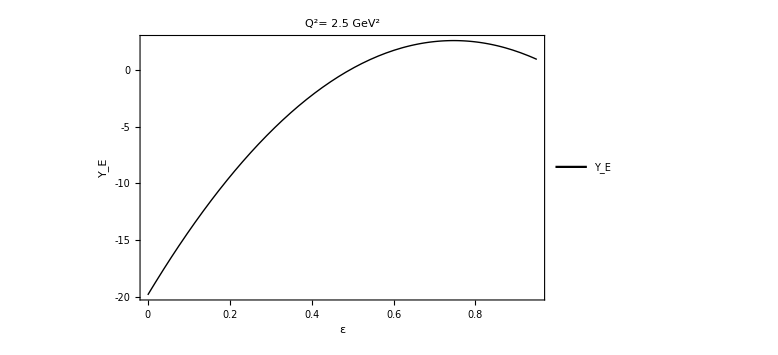

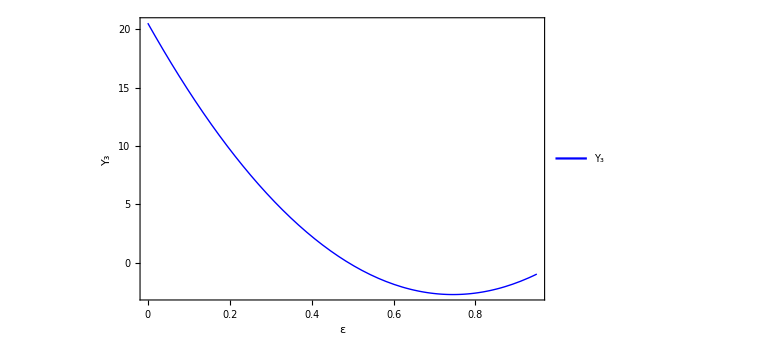

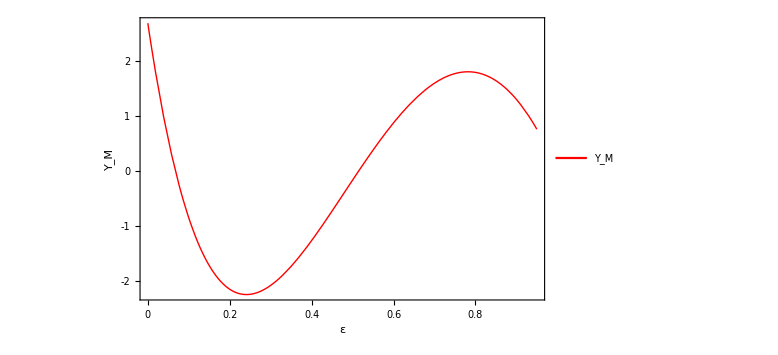

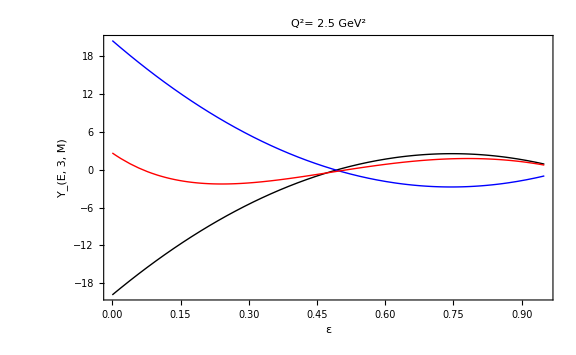

```mathematica
YE=-19.837301245424378+(59.996397704622495*eps)+(-40.15909645919812*eps^2)
Y3=20.515918351208732+(-62.33110920129716*eps)+(41.81519085008843*eps^2)
YM=(YE+(1-R*(2*eps/(1+eps)))*Y3)/R
YEplot=Plot[YE, {eps,0,0.95},PlotStyle->{Black,Thick},FrameLabel->{Style["ε",Bold,16],Style["Y_E",Bold,16]},PlotLegends-> Placed[LineLegend[{"Y_E"},LabelStyle->Directive[22]],{0.92,0.8}], Frame-> True,FrameTicks->All,PlotLabel->Style["Q^2= 2.5 GeV^2",Bold,24], ImageSize-> Large]
Y3plot=Plot[Y3, {eps,0,0.95},PlotStyle->{Blue,Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_3",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_3"},LabelStyle->Directive[22]],{0.92,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]
YMplot=Plot[YM, {eps,0,0.95},PlotStyle->{Red, Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_M",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_M"},LabelStyle->Directive[22]],{0.92,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]

Show[YEplot,Y3plot,YMplot, PlotRange->All,FrameLabel->{Style["ε",Bold,26],Style["Y_(E, 3, M)  ",Bold,24]},Frame-> True,FrameTicks->All,FrameTicksStyle-> Directive[Black,12],ImageSize-> Large]
```

## My Fit

```mathematica
Q2=2.5
fcmuR=1+(-0.11723721716472688)*Q2+(0.0025226146422440594)*(Q2)^2+(-0.0004347472619650877)*(Q2)^3
fcR=fcmuR/2.7972
```

2.5

0.71588

0.255927

```mathematica
epsdata={0.227,0.47,0.63,0.75,0.82,0.913}; 
sigmaRdata={0.015105776,0.015196048,0.01568996,0.016046471,0.016162748,0.016214065};
data=Transpose[{epsdata,sigmaRdata}]
Afc=0.092682494
Bfc=7.794602447
Xfc=0.72242
Lfc=0.36121
Gfc=0.032171428
Rfc=0.2559274891441454

sigmaRfc=Gfc*(1+(eps*Afc) +((Bfc+(eps*Xfc))*(alpha1fc*(eps-1)+alpha2fc*(eps^2-1)))+(Bfc*(1-((eps*2*Rfc)/(1+eps)))+ 2*eps*(1+Lfc))*(beta1fc*(eps-1)+beta2fc*(eps^2-1)))
FindFit[data, {sigmaRfc},{alpha1fc,alpha2fc,beta1fc,beta2fc},eps]
```

{{0.227,0.0151058},{0.47,0.015196},{0.63,0.01569},{0.75,0.0160465},{0.82,0.0161627},{0.913,0.0162141}}

0.0926825

7.7946

0.72242

0.36121

0.0321714

0.255927

0.0321714 (1+0.0926825 eps+(7.7946+0.72242 eps) (alpha1fc (-1+eps)+alpha2fc (-1+eps^2))+(beta1fc (-1+eps)+beta2fc (-1+eps^2)) (2.72242 eps+7.7946 (1-(0.511855 eps)/(1+eps))))

{alpha1fc→60.2785,alpha2fc→-40.2328,beta1fc→-62.6362,beta2fc→41.9007}

```mathematica
alpha1fc=60.27845830484893
alpha2fc=-40.232805884511166
alpha0fc=-(alpha1fc+alpha2fc)
beta1fc=-62.636249918462426
beta2fc=41.90068612661845
beta0fc=-(beta1fc+beta2fc)
```

60.2785

-40.2328

-20.0457

-62.6362

41.9007

20.7356

-20.0457+60.2785 eps-40.2328 eps^2

20.7356-62.6362 eps+41.9007 eps^2

3.90736 (-20.0457+60.2785 eps-40.2328 eps^2+(20.7356-62.6362 eps+41.9007 eps^2) (1-(0.511855 eps)/(1+eps)))

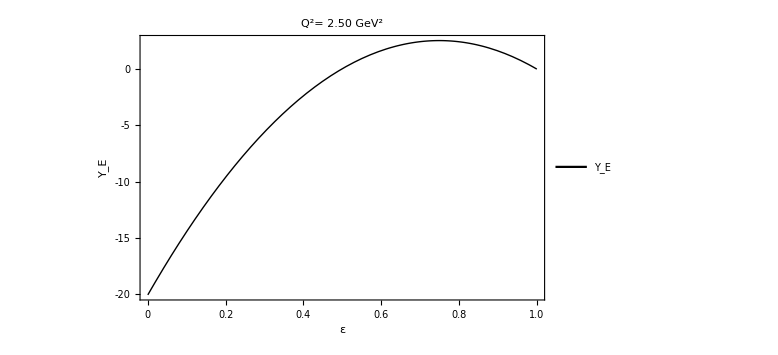

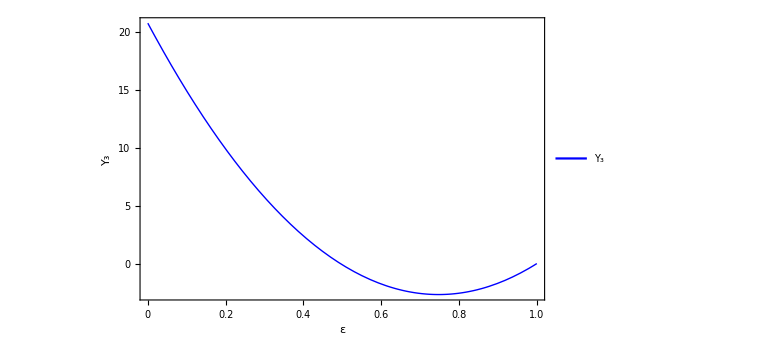

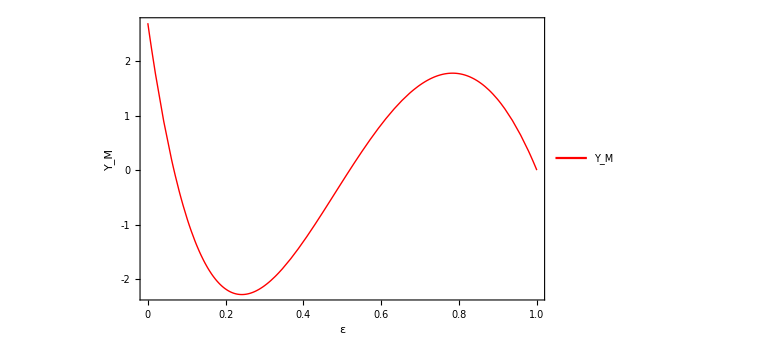

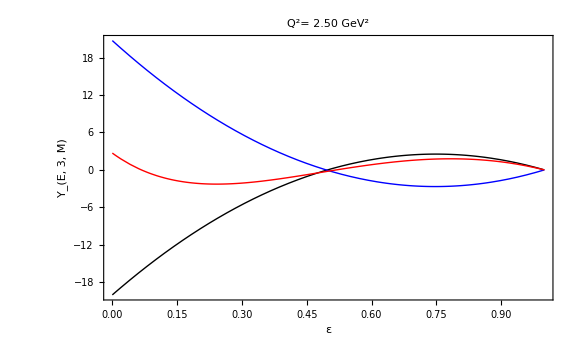

```mathematica
YEfc=-20.045652420337767+(60.27845830484893*eps)+(-40.232805884511166*eps^2)
Y3fc=20.735563791843973+(-62.636249918462426*eps)+(41.90068612661845*eps^2)
YMfc=(YEfc+(1-Rfc*(2*eps/(1+eps)))*Y3fc)/Rfc
YEplotfc=Plot[YEfc, {eps,0,1},PlotStyle->{Black,Thick},FrameLabel->{Style["ε",Bold,16],Style["Y_E",Bold,16]},PlotLegends-> Placed[LineLegend[{"Y_E"},LabelStyle->Directive[22]],{0.9,0.8}], Frame-> True,FrameTicks->All,PlotLabel->Style["Q^2= 2.50 GeV^2",Bold,24], ImageSize-> Large]
Y3plotfc=Plot[Y3fc, {eps,0,1},PlotStyle->{Blue,Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_3",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_3"},LabelStyle->Directive[22]],{0.9,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]
YMplotfc=Plot[YMfc, {eps,0,1},PlotStyle->{Red, Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_M",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_M"},LabelStyle->Directive[22]],{0.9,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]

Show[YEplotfc,Y3plotfc,YMplotfc,PlotRange->All,FrameLabel->{Style["ε",Bold,26],Style["Y_(E, 3, M)  ",Bold,24]},Frame-> True,FrameTicks->All,FrameTicksStyle-> Directive[Black,14],ImageSize-> Large]
```